Melissa Lee
105-128-234
melissaloreleilee@gmail.com
HW 4

```mathematica
(*Problem 1*)
Remove["Global`*"]
$Assumptions={Element[{γ,β,c,t,x,y,z,θ, t',x',y',z',θ'},Reals]&&
β≥0  && β<1 && γ>1 && c > 0  && t≥0 && t'≥0 && δt>=0 && δt'>=0};
λ=({{γ, γ β, 0, 0}, {γ β, γ, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
r=({{c t}, {x}, {y}, {z}});
r'=({{c t'}, {x'}, {y'}, {z'}});
γrule =  γ->1/√(1-β^2) ;
βrule= Solve[γ==1/√(1-β^2),β][[2]];
X' = MatrixForm[Inverse[λ].r];
Print[MatrixForm[r'],"=",X'/.γrule//Simplify]
Print["Boost Operator from lab frame to rocket frame: " MatrixForm[Inverse[λ]/.βrule//Simplify]]
```

(c t'
x'
y'
z')=((c t-x β)/(√(1-β^2))
(x-c t β)/(√(1-β^2))
y
z)

Boost Operator from lab frame to rocket frame:  (γ | -√(-1+γ^2) | 0 | 0
-√(-1+γ^2) | γ | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
(*Problem 2*)
Remove["Global`*"]
$Assumptions={Element[{γ,β,c,t,x,y,z,θ, t',x',y',z',θ'},Reals]&&
β≥0  && β<1 && γ>1 && c > 0  && t≥0 && t'≥0 && δt>=0 && δt'>=0};
L4 = {{γ, γ β, 0, 0},{γ β, γ, 0, 0},{0,0,1,0},{0,0,0,1}};
L2 = γ{{1,β},{ β, 1}};
γrule =  γ->1/√(1-β^2) ; 
βrule= Solve[γ==1/√(1-β^2),β][[2]];
δr' = c δt' {1, Cos[θ'], Sin[θ'] Sin[ϕ'], Sin[θ'] Cos[ϕ']};
δr = L4.δr'/.γrule;
time = δr[[1]]/c//Simplify;
distance = √(δr[[2]]^2+δr[[3]]^2+δr[[4]]^2)//Simplify;
speed=distance/time;
Print["r'=" ,δr']
Print["the speed of the photon in the lab is: ",speed//Simplify]
```

r'={(c δt')/(√(1-β^2))+(c β Cos[θ'] δt')/(√(1-β^2)),(c β δt')/(√(1-β^2))+(c Cos[θ'] δt')/(√(1-β^2)),c Sin[θ'] Sin[ϕ'] δt',c Cos[ϕ'] Sin[θ'] δt'}'

the speed of the photon in the lab is: c

Time Dilation: δt = γ δt'

Simultaneity: δx = -(√(-1+γ^2) δx')/c

Length Contraction: L = L'/γ

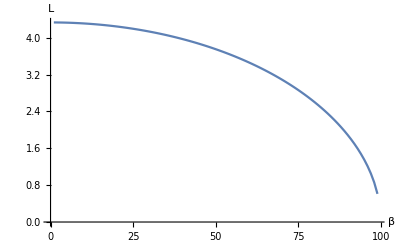

```mathematica
(*Problem 3*)
Remove["Global`*"]
$Assumptions={Element[{γ,β,c,t,x,y,z,θ, t',x',y',z',θ'},Reals]&&
β≥0  && β<1 && γ>1 && c > 0  && t≥0 && t'≥0 && δt>=0 && δt'>=0};
L4 = {{γ, γ β, 0, 0},{γ β, γ, 0, 0},{0,0,1,0},{0,0,0,1}};
L2 = γ{{1,β},{ β, 1}};
γrule =  γ->1/√(1-β^2) ; 
βrule= Solve[γ==1/√(1-β^2),β][[2]];
δr' = {c δt',0,0,0};
δr=L4.δr'/.βrule ;
Print["\nTime Dilation: δt = ",δr[[1]]/c//Simplify]
δr' = {0,δx',0,0};
δr=L4.δr'/.βrule ;
Print["\nSimultaneity: δx = ",δr[[1]]/c//Simplify]
δr' = {c δt', L',0,0};
δr = L4.δr'/.βrule//Simplify;
δt' = δt'/.Solve[δr[[1]]==0,δt'][[1]];  
Print["\nLength Contraction: L = ",δr[[2]]//Simplify]
L'=5 Cos[π/6];
ListLinePlot[Table[δr[[2]]/.γrule,{β,0.01,.99,0.01}],AxesLabel->{"β","L"}]
```

```mathematica
(*Problem 4*)
Remove["Global`*"]
$Assumptions={Element[{γ,β,c,t,x,y,z,θ, t',x',y',z',θ'},Reals]&&
β≥0  && β<1 && γ>1 && c > 0  && t≥0 && t'≥0 && δt>=0 && δt'>=0};
γrule =  γ->1/√(1-β^2) ; 
βrule= Solve[γ==1/√(1-β^2),β][[2]];
x'=L Cos[θ];
t'=x'/u;
β=Vx/c;
t=γ (t'+(Vx x')/c^2)/.γrule//Simplify;
Print["t=",t]
x=γ (x'+Vx t')/.γrule//Simplify;
Print["x=",x]
v1=u;
v2=Vx;
v=(v1+v2)/(1+(v1 v2)/c^2)//Simplify;
Print["v=",v]
β=v/c;
Lrest=x'/γ/.βrule//Simplify;
Print["L=",Lrest]
Print["They differ by a factor of 1/γ."]
```

t=(L (c^2+u Vx) Cos[θ])/(c u √(c^2-Vx^2))

x=(c (L Cos[θ]+Vx ((L (c^2+u Vx) Cos[θ])/(c u √(c^2-Vx^2)))'))/(√(c^2-Vx^2))

v=(u+Vx)/(1+(u Vx)/c^2)

L=(((c (L Cos[θ]+Vx ((L (c^2+u Vx) Cos[θ])/(c u √(c^2-Vx^2)))'))/(√(c^2-Vx^2)))')/γ

They differ by a factor of 1/γ.

```mathematica
(*Problem 5*)
Remove["Global`*"]
$Assumptions={Element[{γ,β,c,t,x,y,z,θ, t',x',y',z',θ'},Reals]&&
β≥0  && β<1 && γ>1 && c > 0  && t≥0 && t'≥0 && δt>=0 && δt'>=0};
L4 = {{γ, γ β, 0, 0},{γ β, γ, 0, 0},{0,0,1,0},{0,0,0,1}};
L2 = γ{{1,β},{ β, 1}};
γrule =  γ->1/√(1-β^2) ; 
βrule= Solve[γ==1/√(1-β^2),β][[2]];
δrp = {c δtp, uxp δtp, uyp δtp, uzp δtp};
δr = {c δt, ux δt, uy δt, uz δt};
δrtemp = L4.δrp;
eqnlist={
δr[[1]] == δrtemp[[1]], 
δr[[2]] == δrtemp[[2]], 
δr[[3]] == δrtemp[[3]],
δr[[4]] == δrtemp[[4]]
}//Simplify;
slist = {δt, ux, uy, uz};
soln=Solve[eqnlist,slist][[1]];
Print["ux = ",ux/.soln]
Print["uy = ",uy/.soln]
Print["uz = ",uz/.soln]
```

ux = (c uxp+c^2 β)/(c+uxp β)

uy = (c uyp)/((c+uxp β) γ)

uz = (c uzp)/((c+uxp β) γ)

```mathematica
(*Problem 6*)
Remove["Global`*"]
$Assumptions={Element[{γ,β,c,t,x,y,z,θ, t',x',y',z',θ'},Reals]&&
β≥0  && β<1 && γ>1 && c > 0  && t≥0 && t'≥0 && δt>=0 && δt'>=0};
L4 = {{γ, γ β, 0, 0},{γ β, γ, 0, 0},{0,0,1,0},{0,0,0,1}};
L2 = γ{{1,β},{ β, 1}};
γrule =  γ->1/√(1-β^2) ; 
βrule= Solve[γ==1/√(1-β^2),β][[2]];
u' = {ut',ux',uy',uz'};
v' = {vt',vx',vy',vz'};
u = L4.u';
v=L4.v';
uv = u[[1]] v[[1]] - (u[[2]] v[[2]] + u[[3]] v[[3]] + u[[4]] v[[4]])/.γrule//Simplify;
Print["ut vt - (ux vx + uy vy + uz vz) = ",uv]
v = {c,vx,vy,vz};
p=γ m v;
Print["P=",{Energy/c,Px,Py,Pz},"=",p]
P2=p.p;
Print["P^2=",P2]
Print["This would not apply to massless objects."]
f[n_]=Series[c m/√(1-n),{n,0,1}];
Print["Taylor Expansion of temporal component:", f[β^2]]
Print["The first term is comparable to classical value of momentum but instead of v it's c."]
```

ut vt - (ux vx + uy vy + uz vz) = ut' vt'-ux' vx'-uy' vy'-uz' vz'

P={Energy/c,Px,Py,Pz}={c m γ,m vx γ,m vy γ,m vz γ}

P^2=c^2 m^2 γ^2+m^2 vx^2 γ^2+m^2 vy^2 γ^2+m^2 vz^2 γ^2

This would not apply to massless objects.

SeriesData::sdatv: First argument β^2 is not a valid variable.

Taylor Expansion of temporal component:c m+1/2 c m β^2+O[β^2]^2

The first term is comparable to classical value of momentum but instead of v it's c.

```mathematica
(*Problem 7*)
Remove["Global`*"]
$Assumptions={Element[{γ,β,c,t,x,y,z,θ, t',x',y',z',θ'},Reals]&&
β≥0  && β<1 && γ>1 && c > 0  && t≥0 && t'≥0 && δt>=0 && δt'>=0};
Graphics3D[{Yellow,Opacity[.5],Cone[{{0,0,3},{0,0,0}},3],Yellow,Opacity[.5],Cone[{{0,0,-3},{0,0,0}},3],Black,Point[{1,0,2}]},ViewPoint->Front]
```

-Graphics3D-